## Get helper functions

```mathematica
NotebookEvaluate[FileNameJoin[{ParentDirectory[ParentDirectory[NotebookDirectory[]]],"UTILITY_readBeamFiles.nb"}]]
```

```mathematica
fileNums = Range[0,20]
fileNames = NotebookDirectory[]<>ToString[#]<>".h5"&/@fileNums
```

{0,1,2,3,4,5}

{/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - random errors/0.h5,/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - random errors/1.h5,/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - random errors/2.h5,/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - random errors/3.h5,/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - random errors/4.h5,/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - random errors/5.h5}

## Process single

```mathematica
data = readBeamFile[fileNames[[1]]];
```

```mathematica
scaledData = {
10^6#x,
10^6#px/#pz,
10^6#y,
10^6#py/#pz,
10^6#z,
10^-9#pz
}&/@data;
```

```mathematica
iqrRangeScale = 4;
```

```mathematica
dataRanges = {
Median[#]-iqrRangeScale*InterquartileRange[#],
Median[#]+iqrRangeScale*InterquartileRange[#]
}&/@Transpose[scaledData]
```

{{-66.2681,87.3096},{-444.532,416.953},{-96.725,58.1079},{-163.568,10.3061},{-84.3681,102.103},{9.46587,10.1771}}

```mathematica
Length[scaledData]
clippedData =Select[
scaledData,
RegionMember[
rangeCuboid = Cuboid[dataRanges[[All,1]],dataRanges[[All,2]]],
#
]&
];
Length[clippedData]
```

99978

92011

```mathematica
imageSize=800;
rasterSize = 800;
```

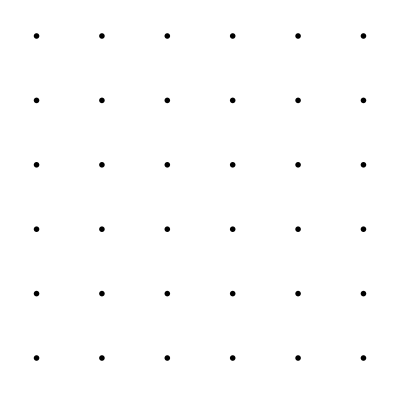

```mathematica
GraphicsGrid[
ParallelTable[
If[i!=j,
Rasterize[
densityHistogramMod[
clippedData[[All,{i,j}]],
{50,50},
ImageSize->imageSize,
PlotRange->{dataRanges[[i]],dataRanges[[j]]},
LabelStyle->20
],RasterSize->rasterSize],
Rasterize[
Histogram[
clippedData[[All,i]],
{(dataRanges[[i,2]]-dataRanges[[i,1]])/50},
ImageSize->imageSize,
PlotRange->{dataRanges[[i]],Automatic},
LabelStyle->20
],RasterSize->rasterSize]
],
{i,1,6},
{j,1,6}
]]
```

## Automate (hold plot ranges constant)

```mathematica
Dynamic[fileName]
imgArr = Table[
data = readBeamFile[fileName];

scaledData = {
10^6#x,
10^6#px/#pz,
10^6#y,
10^6#py/#pz,
10^6#z,
10^-9#pz
}&/@data;

clippedData =Select[
scaledData,
RegionMember[
rangeCuboid = Cuboid[dataRanges[[All,1]],dataRanges[[All,2]]],
#
]&
];

GraphicsGrid[
ParallelTable[
If[i!=j,
Rasterize[
densityHistogramMod[
clippedData[[All,{i,j}]],
{50,50},
ImageSize->imageSize,
PlotRange->{dataRanges[[i]],dataRanges[[j]]},
LabelStyle->20
],RasterSize->rasterSize],
Rasterize[
Histogram[
clippedData[[All,i]],
{(dataRanges[[i,2]]-dataRanges[[i,1]])/50},
ImageSize->imageSize,
PlotRange->{dataRanges[[i]],Automatic},
LabelStyle->20
],RasterSize->rasterSize],
ImageSize->2400
],
{i,1,6},
{j,1,6}
]],

{fileName,fileNames}
];
```

```mathematica
Export[NotebookDirectory[]<>"anim.gif",imgArr,ImageSize->2400]
```

/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - random errors/anim.gif